```mathematica
a= RegionPlot[{(2x≤ 1 && x > y) || 2 ≥ 2x ≥  1 && x < y},{x,0,1},{y,0,1},FrameLabel -> {Style["r_1",FontColor->Black,FontSize->15],Style["r_2",FontColor->Black,FontSize->15]},PlotTheme -> "Scientific",LabelStyle -> Directive[Black,FontFamily -> "Computer Modern",FontSize -> 15],ImageSize -> Large]
b = RegionPlot[{(0 < x < y ≤  1/2) || (1/2 ≤  y < x≤  1)},{x,0,1},{y,0,1},FrameLabel -> {Style["r_1",FontColor->Black,FontSize->15],Style["r_2",FontColor->Black,FontSize->15]},LabelStyle -> Directive[Black,FontFamily -> "Computer Modern",FontSize -> 15],ImageSize -> Large,PlotTheme -> "Scientific"]
c = RegionPlot[{(2x < 1&& 2y > 1) || (2x > 1 && 2y < 1)},{x,0,1},{y,0,1},FrameLabel -> {Style["r_1",FontColor->Black,FontSize->15],Style["r_2",FontColor->Black,FontSize->15]},LabelStyle -> Directive[Black,FontFamily -> "Computer Modern",FontSize -> 15],ImageSize -> Large,PlotTheme -> "Scientific"]


Export["ParamRegion1.png",a]
Export["ParamRegion2.png",b]
```

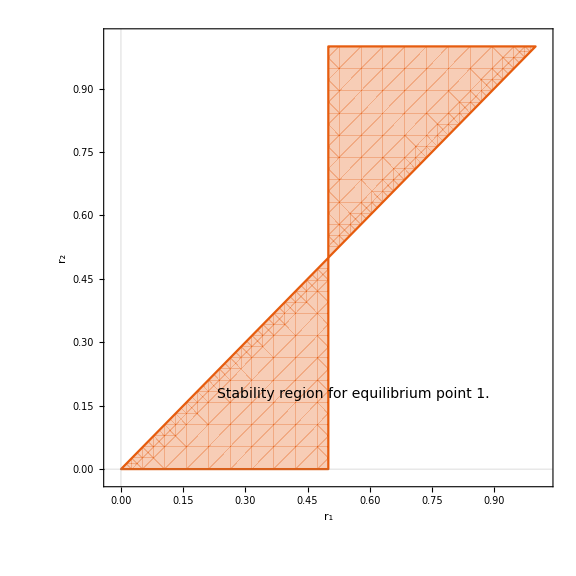

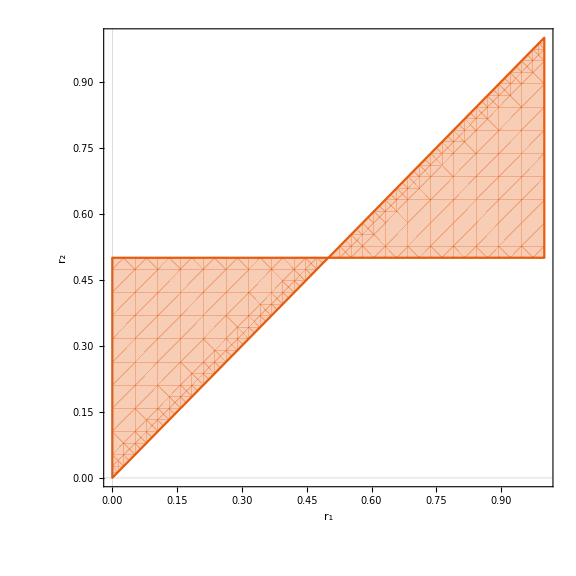

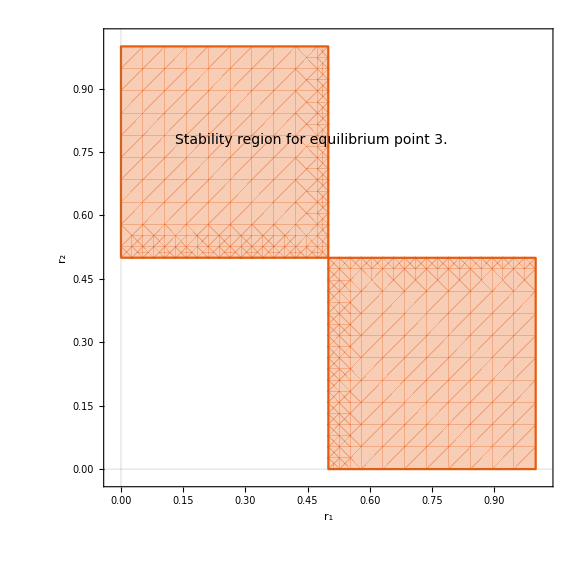

ParamRegion1.png

ParamRegion2.png

ParamRegion1.png

ParamRegion2.png

ParamRegion1.png

ParamRegion2.png